# Лабораторные работы 1–5

## Wolfram Mathematica 10.0

## Лабораторная работа 1. Символьные вычисления

Условия заданий:
1) Раскрыть скобки в выражении:
2) Раскрыть скобки, результат сгруппировать по a:
3) Разложить на множители:
4) Упростить выражение:
5) Найти предел:
6) Вычислить производную:
7) Найти интеграл:
8) Разложить функцию в ряд Тейлора:
9) Найти композицию разложений синуса и косинуса (порядок = 9). Результат записать в нормальной форме:
10) Найти значения сумм и произведений:

```mathematica
(*Задание 1*)
```

```mathematica
Expand[(x-2)^4]
```

16-32 x+24 x^2-8 x^3+x^4

```mathematica
Expand[(x + Cos[x] - Sin[x])^4]
```

x^4+4 x^3 Cos[x]+6 x^2 Cos[x]^2+4 x Cos[x]^3+Cos[x]^4-4 x^3 Sin[x]-12 x^2 Cos[x] Sin[x]-12 x Cos[x]^2 Sin[x]-4 Cos[x]^3 Sin[x]+6 x^2 Sin[x]^2+12 x Cos[x] Sin[x]^2+6 Cos[x]^2 Sin[x]^2-4 x Sin[x]^3-4 Cos[x] Sin[x]^3+Sin[x]^4

```mathematica
(*Задание 2*)
```

```mathematica
Collect[Expand[((x + a)^2 + y)^3], a]
```

a^6+6 a^5 x+x^6+3 x^4 y+3 x^2 y^2+y^3+a^4 (15 x^2+3 y)+a^3 (20 x^3+12 x y)+a^2 (15 x^4+18 x^2 y+3 y^2)+a (6 x^5+12 x^3 y+6 x y^2)

```mathematica
(*Задание 3*)
```

```mathematica
Factor[(x^2 + 2x + 1)*a^3 + (3*y*x^3 + 6*y*x + 3*y)*a^3 + (3*y^2*x^3 + 6*y^2*x + 3*y^2)*a^3 + x^2 * y^3 + 2*x*y^3 + y^3]
```

a^3+2 a^3 x+a^3 x^2+3 a^3 y+6 a^3 x y+3 a^3 x^3 y+3 a^3 y^2+6 a^3 x y^2+3 a^3 x^3 y^2+y^3+2 x y^3+x^2 y^3

```mathematica
Factor[Cos[x]^4 + Sin[x]^4 - 6 * Sin[x]^2 * Cos[x]^2 ]
```

(Cos[x]^2-2 Cos[x] Sin[x]-Sin[x]^2) (Cos[x]^2+2 Cos[x] Sin[x]-Sin[x]^2)

```mathematica
(*Задание 4*)
```

```mathematica
Simplify[(Cos[y]^4+2 Sin[y] Cos[y]^3+Sin[y]^4-2 Cos[y]^2 Sin[y]^2-2 Cos[y] Sin[y]^3)/(Cos[y]^2-Sin[y]^2) - 2Cos[y]Sin[y]]
```

Cos[2 y]

```mathematica
(*Задание 5*)
```

```mathematica
Limit[(1+x)^(1/x), x->0]
```

ⅇ

```mathematica
Limit[(1+1/x)^x,x->Infinity]
```

ⅇ

```mathematica
Limit[Exp[α Sin[x]],x->Infinity]
```

ⅇ^(α Interval[{-1,1}])

```mathematica
Limit[Sin[x]/x,x->0]
```

1

```mathematica
Limit[(a^x-1)/x,x->0]
```

Log[a]

```mathematica
Limit[1/x,x->-Infinity]
```

0

```mathematica
(*Задание 6*)
```

```mathematica
D[Sin[x], x]
```

Cos[x]

```mathematica
D[f[g[x]], x]
```

f'[g[x]] g'[x]

```mathematica
D[Sin[x y], {x, 2},{y, 1}]
```

-x y^2 Cos[x y]-2 y Sin[x y]

```mathematica
D[Log[(x-3)/(x+3)], {x, 2}]
```

((3+x) ((2 (-3+x))/(3+x)^3-2/(3+x)^2))/(-3+x)+(-(-3+x)/(3+x)^2+1/(3+x))/(-3+x)-((3+x) (-(-3+x)/(3+x)^2+1/(3+x)))/(-3+x)^2

```mathematica
(*Задание 7*)
```

```mathematica
Integrate[x^2/(x+a)^3, x]
```

(a (3 a+4 x))/(2 (a+x)^2)+Log[a+x]

```mathematica
Integrate[x^2/Sqrt[a x+b], x]
```

(2 √(b+a x) (8 b^2-4 a b x+3 a^2 x^2))/(15 a^3)

```mathematica
Integrate[Sin[a x]/x, {x, -Infinity, Infinity}]
```

ConditionalExpression[π Sign[a],a∈Reals]

```mathematica
Integrate[x  Sin[a x] / (x^2 + b^2), {x, -Infinity, Infinity}]
```

ConditionalExpression[(a ⅇ^(-Abs[a]/(√(1/b^2))) π)/Abs[a],a∈Reals&&(Re[b^2]≥0||b^2∉Reals)]

```mathematica
Integrate[x Exp(a x) Sin[b x], x]
```

a Exp (-((-2+b^2 x^2) Cos[b x])/b^3+(2 x Sin[b x])/b^2)

```mathematica
Integrate[ArcSin[x], x]
```

√(1-x^2)+x ArcSin[x]

```mathematica
Integrate[Sin[a x]/x, {x, -Infinity, Infinity}, Assumptions->{a>0} ]
```

π

```mathematica
Integrate[x Sin[a x]/(x^2 + b^2), {x, -Infinity, Infinity}, Assumptions->{a>0, b>0} ]
```

ⅇ^(-a b) π

```mathematica
(*Задание 8*)
```

```mathematica
Series[E^x, {x, 0, 7}]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+O[x]^8

```mathematica
Series[Sqrt[x],{x,4,5}]
```

2+(x-4)/4-1/64 (x-4)^2+1/512 (x-4)^3-(5 (x-4)^4)/16384+(7 (x-4)^5)/131072+O[x-4]^6

```mathematica
Series[Sin[Sin[x]],{x,0,5}]
```

x-x^3/3+x^5/10+O[x]^6

```mathematica
Series[Tan[x],{x,0,9}]
```

x+x^3/3+(2 x^5)/15+(17 x^7)/315+(62 x^9)/2835+O[x]^10

```mathematica
InverseSeries[Series[Tan[x],{x,0,9}]]
```

x-x^3/3+x^5/5-x^7/7+x^9/9+O[x]^10

```mathematica
(*Задание 9*)
```

```mathematica
Series[Cos[Sin[x]], {x, 0, 9}] // Normal
```

1-x^2/2+(5 x^4)/24-(37 x^6)/720+(457 x^8)/40320

```mathematica
(*Задание 10*)
```

```mathematica
Sum[1/n^2,{n,1,Infinity}]
```

π^2/6

```mathematica
Sum[Sin[n x]/n,{n,1,Infinity}]
```

1/2 ⅈ (Log[1-ⅇ^(ⅈ x)]-Log[ⅇ^(-ⅈ x) (-1+ⅇ^(ⅈ x))])

```mathematica
Sum[1/n^5,{n,1,Infinity}]
```

Zeta[5]

```mathematica
Product[1-x^2/(n^2 Pi^2), {n, 1, Infinity}]
```

Sinc[x]

#d

## Лабораторная работа 2. Графики и решение уравнений

Условия заданий:
1) График функции на отрезке от 0 до 1:
2) График поверхности:
3) Решить уравнения:
4) Численное решение уравнений:
5) Решить систему:
6) Численное решение системы:
7) Дифференциальные уравнения:
8) Системы дифференциальных уравнений (аналитически):
9) Уравнение маятника и график решения:

```mathematica
(*Задание 1*)
```

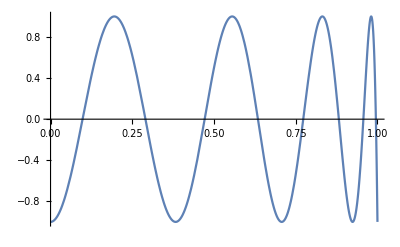

```mathematica
Plot[1 - 2*(1 - 2*(1 - 2*(1 - 2*x^2)^2)^2)^2, {x, 0, 1}]
```

```mathematica
(*Задание 2*)
```

```mathematica
Plot3D[Sin[x/(y + Pi/10)], {x, 0, 2 Pi}, {y, 0, Pi/2},
 PlotPoints -> 40, AxesLabel -> {"X", "Y", "Z"}]
```

-Graphics3D-

```mathematica
(*Задание 3*)
```

```mathematica
Solve[Log[x + Sqrt[x^2 + a]] == b, x]
```

{{x→1/2 ⅇ^-b (-a+ⅇ^(2 b))}}

```mathematica
Solve[Log[Sqrt[x]] == Sqrt[Log[x]], x]
```

{{x→1},{x→ⅇ^4}}

```mathematica
Solve[x^4 - 5 x^2 - 3 == 0, x]
```

{{x→-ⅈ √(1/2 (-5+√37))},{x→ⅈ √(1/2 (-5+√37))},{x→-√(1/2 (5+√37))},{x→√(1/2 (5+√37))}}

```mathematica
Solve[x^3 - 3 x - 1 == 0, x]
```

{{x→1/(1/2 (1+ⅈ √3))^(1/3)+(1/2 (1+ⅈ √3))^(1/3)},{x→-1/2 (1-ⅈ √3) (1/2 (1+ⅈ √3))^(1/3)-(1/2 (1+ⅈ √3))^(2/3)},{x→-(1-ⅈ √3)/(2^(2/3) (1+ⅈ √3)^(1/3))-(1+ⅈ √3)^(4/3)/(2 2^(1/3))}}

```mathematica
Solve[Cos[x] == Tan[x], x]
```

```mathematica
{{x->ConditionalExpression[π-ArcTan[√(1/2 (-1+√5))]+2 π C[1],C[1]∈Integers]},{x->ConditionalExpression[ArcTan[√(1/2 (-1+√5))]+2 π C[1],C[1]∈Integers]},{x->ConditionalExpression[ArcTan[-ⅈ √(1/2 (1+√5)),1/2 (-1-√5)]+2 π C[1],C[1]∈Integers]},{x->ConditionalExpression[ArcTan[ⅈ √(1/2 (1+√5)),1/2 (-1-√5)]+2 π C[1],C[1]∈Integers]}}
```

{{x→ConditionalExpression[π-ArcTan[√(1/2 (-1+√5))]+2 π C[1], C[1]∈ℤ]},{x→ConditionalExpression[ArcTan[√(1/2 (-1+√5))]+2 π C[1], C[1]∈ℤ]},{x→ConditionalExpression[ArcTan[-ⅈ √(1/2 (1+√5)),1/2 (-1-√5)]+2 π C[1], C[1]∈ℤ]},{x→ConditionalExpression[ArcTan[ⅈ √(1/2 (1+√5)),1/2 (-1-√5)]+2 π C[1], C[1]∈ℤ]}}

```mathematica
Solve[a*x^4 + b*x^3 + 1 == 0, x]
```

{{x→-b/(4 a)+1/2 √(b^2/(4 a^2)+(4 (2/3)^(1/3))/((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))+((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))/(2^(1/3) 3^(2/3) a))-1/2 √(b^2/(2 a^2)-(4 (2/3)^(1/3))/((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))-((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))/(2^(1/3) 3^(2/3) a)-b^3/(4 a^3 √(b^2/(4 a^2)+(4 (2/3)^(1/3))/((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))+((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))/(2^(1/3) 3^(2/3) a))))},{x→-b/(4 a)+1/2 √(b^2/(4 a^2)+(4 (2/3)^(1/3))/((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))+((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))/(2^(1/3) 3^(2/3) a))+1/2 √(b^2/(2 a^2)-(4 (2/3)^(1/3))/((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))-((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))/(2^(1/3) 3^(2/3) a)-b^3/(4 a^3 √(b^2/(4 a^2)+(4 (2/3)^(1/3))/((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))+((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))/(2^(1/3) 3^(2/3) a))))},{x→-b/(4 a)-1/2 √(b^2/(4 a^2)+(4 (2/3)^(1/3))/((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))+((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))/(2^(1/3) 3^(2/3) a))-1/2 √(b^2/(2 a^2)-(4 (2/3)^(1/3))/((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))-((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))/(2^(1/3) 3^(2/3) a)+b^3/(4 a^3 √(b^2/(4 a^2)+(4 (2/3)^(1/3))/((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))+((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))/(2^(1/3) 3^(2/3) a))))},{x→-b/(4 a)-1/2 √(b^2/(4 a^2)+(4 (2/3)^(1/3))/((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))+((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))/(2^(1/3) 3^(2/3) a))+1/2 √(b^2/(2 a^2)-(4 (2/3)^(1/3))/((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))-((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))/(2^(1/3) 3^(2/3) a)+b^3/(4 a^3 √(b^2/(4 a^2)+(4 (2/3)^(1/3))/((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))+((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))/(2^(1/3) 3^(2/3) a))))}}

```mathematica
(*Задание 4*)
```

```mathematica
NSolve[x^7 + 7*x == 7, x]
```

{{x→-1.3217-0.706695 ⅈ},{x→-1.3217+0.706695 ⅈ},{x→-0.137797-1.43289 ⅈ},{x→-0.137797+1.43289 ⅈ},{x→0.920191},{x→0.999402-0.797172 ⅈ},{x→0.999402+0.797172 ⅈ}}

```mathematica
FindRoot[Cos[x] - x, {x, 1}]
```

{x→0.739085}

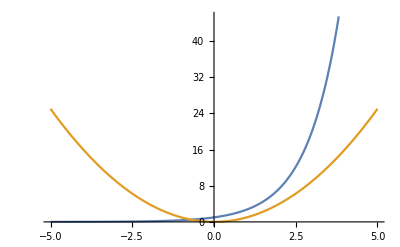

```mathematica
Plot[{E^x, x^2}, {x, -5, 5}]
```

```mathematica
FindRoot[E^2 - x^2, {x, -0.7}]
```

{x→-2.71828}

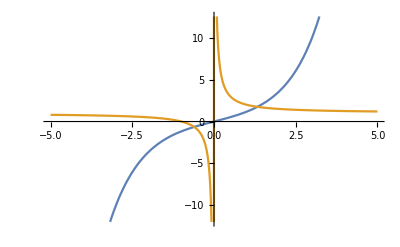

```mathematica
Plot[{Sinh[x], 1 + 1/x}, {x, -5, 5}]
```

```mathematica
FindRoot[Sinh[x] == 1 + 1/x, {x, 1.3}]
```

{x→1.32752}

```mathematica
FindRoot[Sinh[x] == 1 + 1/x, {x, -0.6}]
```

{x→-0.607635}

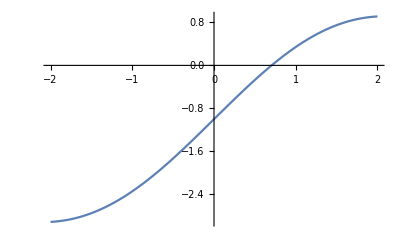

```mathematica
Plot[Sin[x] - 1 + x/2, {x, -2, 2}]
```

```mathematica
FindRoot[Sin[x] + x/2 - 1, {x, 0.7}]
```

{x→0.704577}

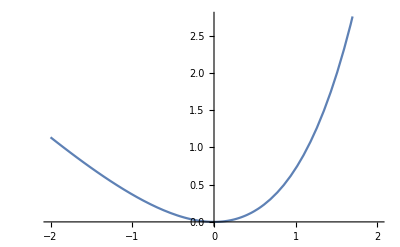

```mathematica
Plot[E^x - x - 1, {x, -2, 2}]
```

```mathematica
FindRoot[E^x - x - 1, {x, 0}]
```

{x→0.}

```mathematica
(*Задание 5*)
```

```mathematica
solution = Solve[{x + y == 5, x - y == 1}, {x, y}]
```

{{x→3,y→2}}

```mathematica
{x + y == 5, x - y == 1} /. solution
```

{{True,True}}

```mathematica
Solve[{Sqrt[x + y] == Sqrt[x y], x^2 + y^2 == 1}, {x, y}]
```

{{x→1/2 (1-√2+√(-1+2 √2)),y→1/2 (1-√2-√(-1+2 √2))},{x→1/2 (1-√2-√(-1+2 √2)),y→1/2 (1-√2+√(-1+2 √2))},{x→1/2+1/(√2)+1/2 ⅈ √(1+2 √2),y→1/2+1/(√2)-1/2 ⅈ √(1+2 √2)},{x→1/2+1/(√2)-1/2 ⅈ √(1+2 √2),y→1/2+1/(√2)+1/2 ⅈ √(1+2 √2)}}

```mathematica
Solve[{Sin[x + y] == Cos[x - y], Tan[x y] == Cos[x y]}]
```

{{x→(4 ArcCos[-√(1/2 (-1+√5))])/π,y→π/4},{x→(4 ArcCos[√(1/2 (-1+√5))])/π,y→π/4},{x→(4 ArcCos[-ⅈ √(1/2 (1+√5))])/(3 π),y→-(3 π)/4},{x→(4 ArcCos[ⅈ √(1/2 (1+√5))])/(3 π),y→-(3 π)/4},{x→π/4,y→(4 ArcCos[-√(1/2 (-1+√5))])/π},{x→π/4,y→(4 ArcCos[√(1/2 (-1+√5))])/π},{x→-(3 π)/4,y→(4 ArcCos[-ⅈ √(1/2 (1+√5))])/(3 π)},{x→-(3 π)/4,y→(4 ArcCos[ⅈ √(1/2 (1+√5))])/(3 π)}}

```mathematica
(*Задание 6*)
```

```mathematica
f[z_?NumericQ] := x^2 + y^2 - Sinh[z] /.
 FindRoot[{x^2 + y^2 - z^2 == 1, x + y == z}, {{x, 1}, {y, 1}}]
```

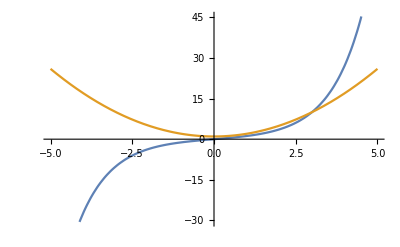

```mathematica
Plot[{Sinh[z], 1 + z^2}, {z, -5, 5}]
```

```mathematica
solutionZ = FindRoot[f[z] == 0, {z, 3}]
```

{0.848636→1.44364}

```mathematica
Solve[{x + y == z, x^2 + y^2 == 1 + z^2} /. solutionZ, {x, y}]
```

{{x→0.13952,y→1.30412},{x→1.30412,y→0.13952}}

```mathematica
(*Задание 7*)
```

```mathematica
DSolve[y''[x] x^2 + 5 y'[x] x + y[x] == 0, y[x], x] // Simplify
```

{{y[x]→x^(-2-√3) (C[1]+x^(2 √3) C[2])}}

```mathematica
DSolve[y''[x] x^2 + 3 y'[x] x + y[x] == Sin[2 x], y[x], x]
```

{{y[x]→C[1]/x-CosIntegral[2 x]/(2 x)+(C[2] Log[x])/x}}

```mathematica
DSolve[{y''[x] x^2 + 5 y'[x] x + y[x] == Power[x, -2 + Sqrt[3]], y[1] == -1/12, y'[1] == 1/12 (2 + Sqrt[3])}, y[x], x]
```

{{y[x]→1/12 x^(-2+√3) (-1+2 √3 Log[x])}}

```mathematica
TraditionalForm[DSolve[y''[x] + y[x]/Sin[x]^2 == 0, y[x], x]]
```

{{y(x)→c_1 (cos^2(x)-1)^(1/4) -1/2(ⅈ √3)/2cos(x)+c_2 (cos^2(x)-1)^(1/4) -1/2(ⅈ √3)/2cos(x)}}

```mathematica
(*Задание 8*)
```

```mathematica
DSolve[{x'[t] == t^2 + y[t], y'[t] == x[t]}, {x[t], y[t]}, t] // FullSimplify
```

{{x[t]→-2 t+C[1] Cosh[t]+C[2] Sinh[t],y[t]→-2-t^2+C[2] Cosh[t]+C[1] Sinh[t]}}

```mathematica
DSolve[{y''[t] == 4 x[t] - 5 y[t], x''[t] == 4 y[t] - 5 x[t], y[0] == 1, x[0] == 0, y'[0] == 0, x'[0] == 1}, {x[t], y[t]}, t] // FullSimplify
```

{{x[t]→1/6 (3 (Cos[t]-Cos[3 t]+Sin[t])+Sin[3 t]),y[t]→1/2 (Cos[t]+Cos[3 t])+(2 Sin[t]^3)/3}}

```mathematica
(*Задание 9*)
```

```mathematica
sol = NDSolve[{x''[t] == -Sin[x[t]], x[0] == 0, x'[0] == 1.999}, x, {t, -100, 100}]
```

{{x→InterpolatingFunction[{{-100., 100.}}, <>]}}

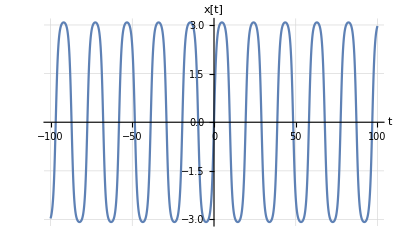

```mathematica
Plot[x[t] /. sol, {t, -100, 100}, AxesLabel -> {"t", "x[t]"}, GridLines -> Automatic]
```

## Лабораторная работа 3. Целочисленные задачи и поиск минимума

Условия заданий:
1) Проверить тождество для сумм и упростить сумму.
2) Найти сумму Sum[i^k, {i, 0, n}].
3) Найти степень вхождения 5 в 10000!.
4) Найти количество простых чисел среди чисел Фибоначчи.
5) Найти совершенные числа на заданном промежутке.
6) Доказать неравенство о средних с помощью Reduce.
7) Найти минимум функции с помощью FindMinimum.

```mathematica
(*Задание 1*)
lhs = Sum[k, {k, 1, n}]^2;
rhs = Sum[k^3, {k, 1, n}];
Simplify[lhs == rhs]
```

True

```mathematica
Sum[k/(k^4 + k^2 + 1), {k, 1, n}] // Simplify
```

(n (1+n))/(2 (1+n+n^2))

```mathematica
(*Задание 2*)
```

```mathematica
Sum[i^k, {i, 0, n}]
```

0^k+HarmonicNumber[n,-k]

```mathematica
(*Задание 3*)
IntegerExponent[10000!, 5]
```

2499

```mathematica
(*Задание 4*)
```

```mathematica
Length[Select[Fibonacci[Range[1000]], PrimeQ]]
```

21

```mathematica
(*Задание 5*)
Select[Range[1000], Total[Most[Divisors[#]]] == # &]
```

{6,28,496}

```mathematica
(*Задание 6*)
Reduce[(a + b)/2 ≥ Sqrt[a*b] && a ≥ 0 && b ≥ 0, {a, b}, Reals]
```

a≥0&&b≥0

```mathematica
(*Задание 7*)
FindMinimum[Exp[x] + 1.2/x, {x, 1, 2}]
```

{3.71698,{x→0.752098}}

```mathematica
Directory[]
```

C:\Users\LENOVOL\Documents

## Лабораторная работа 4. Списки, матрицы, изображения

Условия заданий:
1) Задать список 1, 2, 3, 4, 5.
2) Сформировать список от 4 до 15 с шагом 2.
3) Задать список 1, 2, 3, 4, 5: добавить a перед первым элементом, вставить 25 после 5, вывести первые два элемента, удалить элементы на нечетных местах, остальные возвести в квадрат, вывести второй и четвертый элементы.
4) Задать матрицу 3x3: определитель, собственные значения, собственные векторы, транспонирование.
5) Задать две матрицы 3x3: сложение, транспонирование, обратные матрицы, произведение.
6) Открыть картинку, вывести ее в Mathematica, создать рабочую директорию и показать ее содержимое.

```mathematica
(*Задание 1*)
```

```mathematica
list1 = Range[5]
```

{1,2,3,4,5}

```mathematica
(*Задание 2*)
```

```mathematica
list2 = Table[4 + 2 k, {k, 0, 5}]
```

{4,6,8,10,12,14}

```mathematica
(*Задание 3*)
```

```mathematica
list3={1,2,3,4,5};

list3=Prepend[list3,a]

list3=Insert[list3,25,Position[list3,5] + 1]

Take[list3,2]

(*Удаляем элементы на нечётных номерах (1-й,3-й,5-й,...)*)
list3=Delete[list3,Table[{i},{i,1,Length[list3],2}]]

(*Возводим оставшиеся элементы в квадрат*)
list3=list3^2

(*Выводим второй и четвёртый элемент*)

If[Length[list3]≥4,{list3[[2]],list3[[4]]},{list3[[2]],"четвёртого элемента нет"}]
```

{a,1,2,3,4,5}

{a,1,2,3,4,5,25}

{a,1}

{1,3,5}

{1,9,25}

{9,четвёртого элемента нет}

```mathematica
(*Задание 4*)
```

```mathematica
(*Произвольная матрица 3×3*)M={{2,1,0},{1,3,1},{0,1,2}};

(*Определитель*)
Det[M]
(*8*)

(*Собственные значения*)
Eigenvalues[M]

(*Собственные векторы*)
Eigenvectors[M]

(*Транспонирование*)
Transpose[M]
```

8

{4,2,1}

{{1,2,1},{-1,0,1},{1,-1,1}}

{{2,1,0},{1,3,1},{0,1,2}}

```mathematica
(*Задание 5*)
```

```mathematica
A={{1,2,3},{4,5,6},{7,8,10}};
B={{2,0,1},{1,3,0},{0,1,4}};

(*Сложение*)
A+B

(*Транспонирование каждой*)
Transpose[A]
Transpose[B]

(*Обратные матрицы*)
Inverse[A]
Inverse[B]

(*Перемножение A и B*)
A.B

(*Перемножение B и A (для проверки некоммутативности)*)
B.A
```

{{3,2,4},{5,8,6},{7,9,14}}

{{1,4,7},{2,5,8},{3,6,10}}

{{2,1,0},{0,3,1},{1,0,4}}

{{-2/3,-4/3,1},{-2/3,11/3,-2},{1,-2,1}}

{{12/25,1/25,-3/25},{-4/25,8/25,1/25},{1/25,-2/25,6/25}}

{{4,9,13},{13,21,28},{22,34,47}}

{{9,12,16},{13,17,21},{32,37,46}}

```mathematica
(*Задание 6*)
```

```mathematica
workDir = Directory[]
```

```mathematica
"C:\\Users\\pnvk\\Documents"
```

```mathematica
Image[test_img.png]
```

```mathematica
img = Import["test_img.png"];
Image[img]
```

```mathematica
Export["123.txt", 123]
```

```mathematica
"123.txt"
```

123.txt

## Лабораторная работа 5. Операции со списками

Условия заданий:
1) Элементы на четных номерах возвести в куб.
2) Элементы на нечетных номерах возвести в четвертую степень.
3) Элементы на нечетных номерах заменить на q.
4) Элементы на четных номерах заменить на t.
5) Удалить из списка значения 3 и 6.
6) Удалить два последних значения.
7) Удалить первые два значения.
8) Заменить пятый элемент на 100.
9) Добавить в список число 9 перед первым элементом.
10) Добавить в список число 10 после последнего элемента.
11) Вывести значение, стоящее на седьмом месте.
12) У вектора X удалить все нечетные числа.
13) Удалить из вектора X все числа с четными индексами.
14) Найти и вывести пять первых многочленов Лежандра.

```mathematica
list={12,3,21,1,6,72,4,90,33};

(*1) Элементы на четных номерах в куб*)
MapAt[Cube,list,List/@Select[Range[Length[list]],EvenQ]]

(*2) Элементы на нечетных номерах в четвертую степень*)
MapAt[#^4&,list,List/@Select[Range[Length[list]],OddQ]]

(*3) Элементы на нечетных номерах заменить на q*)
MapAt["q"&,list,List/@Select[Range[Length[list]],OddQ]]

(*4) Элементы на четных номерах заменить на t*)
MapAt["t"&,list,List/@Select[Range[Length[list]],EvenQ]]

(*5) Удалить из списка 3 и 6 значения (удаляем значения,равные 3 и 6)*)
DeleteCases[list,3|6]

(*6) Удалить два последних значения*)
Drop[list,-2]

(*7) Удалить первые два значения из списка*)
Drop[list,2]

(*8) Заменить 5 элемент на 100*)
ReplacePart[list,5->100]

(*9) Добавить в список число 9 перед первым элементом*)
Prepend[list,9]

(*10) Добавить в список число 10 после последнего элемента*)
Append[list,10]

(*11) Вывести значение,стоящее на 7-ом месте*)
list[[7]]

(*12) У вектора X удалить все нечетные числа*)
X={12,3,21,1,6,72,4,90,33};
Select[X,EvenQ]

(*13) Удалить из вектора X все числа с четными индексами*)
X={12,3,21,1,6,72,4,90,33};
Delete[X,List/@Select[Range[Length[X]],EvenQ]]

(*14) Найти и вывести на экран пять первых многочленов Лежандра*)
Table[LegendreP[n,x],{n,0,4}]
```

{20736,3,194481,1,1296,72,256,90,1185921}

{q,3,q,1,q,72,q,90,q}

{12,t,21,t,6,t,4,t,33}

{12,21,1,72,4,90,33}

{12,3,21,1,6,72,4}

{21,1,6,72,4,90,33}

{12,3,21,1,100,72,4,90,33}

{9,12,3,21,1,6,72,4,90,33}

{12,3,21,1,6,72,4,90,33,10}

4

{12,6,72,4,90}

{12,21,6,4,33}

{1,x,1/2 (-1+3 x^2),1/2 (-3 x+5 x^3),1/8 (3-30 x^2+35 x^4)}